```mathematica
Remove[r,theta,x1,x2,mu,omega]
(*
sol = Solve[{mu*r==r^3,omega+nu*r^2==0},{r,nu,omega}]

r = r/.sol[[3]]

thetaP = omega+nu*r^2
*)
x1'[t] = 1/10*x1[t]-x2 [t]^3-x1[t]*x2[t]^2-x1[t]^2*x2[t]-x2[t]-x1[t]^3;
x2'[t] = x1[t]+1/10*x2[t]+x1[t]*x2[t]^2+x1[t]^3-x2[t]^3-x1[t]^2*x2[t];

J={{D[x1'[t],x1[t]], D[x1'[t],x2[t]]},{D[x2'[t],x1[t]],D[x2'[t],x2[t]]}};
Det[J];
Eigenvalues[J];

r'[t] = mu*r[t]-r[t]^3;
theta'[t]=omega+nu*r[t]^2;
Jr = {{D[r'[t],r[t]],D[r'[t],theta[t]]},{D[theta'[t],r[t]],D[theta'[t],theta[t]]}};
Det[Jr];
Eigenvalues[Jr];

x1[t] = r[t]*cos[theta];
x2[t] = r[t]*sin[theta];
Jxr = {{D[x1'[t],r[t]],D[x1'[t],theta[t]]},{D[x2'[t],r[t]],D[x2'[t],theta[t]]}};
Det[Jxr];
Eigenvalues[Jxr];

r[t] = Sqrt[i^2+j^2];
r'[t];
Jr = {{D[r'[t],i],D[r'[t],j]},{D[theta'[t],i],D[theta'[t],j]}};
Det[Jr];
Eigenvalues[Jr];
```

{{y→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

{InterpolatingFunction[…][t]}

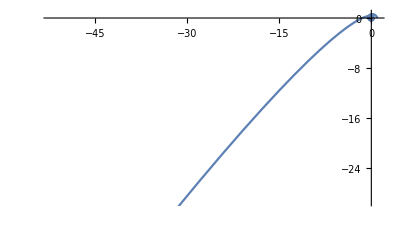

```mathematica
Remove[x1,x2]
s=NDSolve[{x1'[t] == 1/10*x1[t]-x2 [t]^3-x1[t]*x2[t]^2-x1[t]^2*x2[t]-x2[t]-x1[t]^3,
		x2'[t] == x1[t]+1/10*x2[t]+x1[t]*x2[t]^2+x1[t]^3-x2[t]^3-x1[t]^2*x2[t],x1[0]==1,x2[0]==0},{x1,x2},{t,10}]
x1[t]/.s
ParametricPlot[Evaluate[{x1[t],x2[t]}/. s],{t,0,20}]
```